## NF theory for two unstable modes

```mathematica
eval=Thread[{kba,kbc,kcb,kab,kac,μ,β,v1,v2,v3,da,db,n}->{3.,3.,3.,100,100,0.0076,0.09,70,100,40,1,0.0008,2}];
```

```mathematica
ha[m_,k_]:=m^n/(m^n+k^n)
hi[m_,k_]:=k^n/(m^n+k^n)
```

```mathematica
f[a_,b_,c_]:=v1 (*ha[a,kaa]*)hi[b,kba]-μ a+β
g[a_,b_,c_]:=v2 ha[a,kab]hi[c,kcb]-μ b+β
h[a_,b_,c_]:=v3 hi[a,kac]hi[b,kbc](*ha[c,kcc]*)-μ c+β
```

```mathematica
fp=Flatten[NSolve[{f[a0,b0,c0],g[a0,b0,c0],h[a0,b0,c0]}/.eval,{a0,b0,c0},Reals]]
```

{b0→41.7803,c0→31.8528,a0→59.0866}

```mathematica
zeros=Thread[{a,b,c}->ConstantArray[0,3]];
```

```mathematica
j=D[{f[a+a0,b+b0,c+c0],g[a+a0,b+b0,c+c0],h[a+a0,b+b0,c+c0]},{{a,b,c}}]/.eval/.fp/.zeros;
jd=j-k^2DiagonalMatrix[{da,db,0}];
```

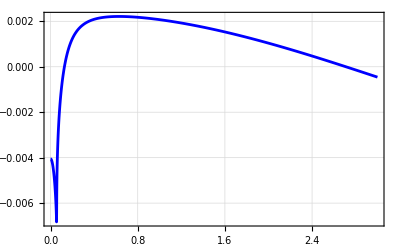

```mathematica
Plot[Max[Re[Eigenvalues[jd]/.eval]],{k,0,3},PlotRange->All,PlotStyle->Blue,Frame->True,GridLines->Automatic]
```

#### Numerical solution

```mathematica
T=700;
δ=10;
```

```mathematica
eqn={1/δ D[a[t,x],{t,1}]==da D[a[t,x],{x,2}]+f[a[t,x]+a0,b[t,x]+b0,c[t,x]+c0],1/δ D[b[t,x],{t,1}]==db D[b[t,x],{x,2}]+g[a[t,x]+a0,b[t,x]+b0,c[t,x]+c0],1/δ D[c[t,x],{t,1}]==h[a[t,x]+a0,b[t,x]+b0,c[t,x]+c0]}/.eval/.fp;
ic={a[0,x]==0.01(Cos[x]+2Cos[2x]),b[0,x]==0.01(Cos[x]+2Cos[2x]),c[0,x]==0.01Cos[x]+0.2Cos[2x]};
bc={a[t,-Pi]==a[t,Pi],b[t,-Pi]==b[t,Pi],c[t,-Pi]==c[t,Pi]};
{asol,bsol,csol}=NDSolveValue[{eqn,ic,bc},{a,b,c},{t,0,T},{x,-Pi,Pi}];
```

```mathematica
ListAnimate[Table[Plot[{asol[t,x],-bsol[t,x],csol[t,x]},{x,-Pi,Pi},PlotRange->{-100,100}],{t,0,T,20}]]
```

```mathematica
data=Table[Table[1/Pi NIntegrate[Cos[k x]bsol[t,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,1,T,5}],{k,1,4}];
```

```mathematica
data2=Table[Table[1/Pi NIntegrate[Cos[k x]csol[t,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,1,T,5}],{k,1,4}];
```

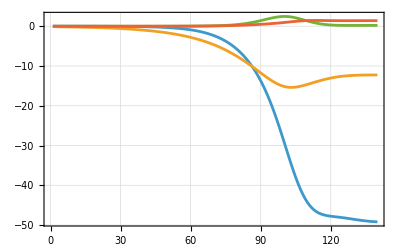

```mathematica
ListLinePlot[data[[1;;4]],PlotRange->All,Frame->True,GridLines->Automatic]
```

#### Fitting to NF equations

```mathematica
z=-data[[1]];
```

```mathematica
times=Table[i,{i,Dimensions[z][[1]]}];
ztofit=Table[{times[[i]],z[[i]]},{i,Dimensions[z][[1]]}];
```

```mathematica
rsol=DSolve[{r'[x]==p1 r[x]-p2 r[x]^3,r[0]==r0},r[x],x,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[x]/.rsol[[1,1]]
```

(ⅇ^(p1 x) √p1 r0)/(√(p1-p2 r0^2) √(1+(ⅇ^(2 p1 x) p2 r0^2)/(p1-p2 r0^2)))

```mathematica
fit=NonlinearModelFit[ztofit,functofit,{{r0,0.01},{p1,01},{p2,0.002}},x]
```

FittedModel[…]

```mathematica
param=fit["BestFitParameters"]
```

{r0→0.00280182,p1→0.0948893,p2→0.0000395659}

```mathematica
p=Plot[functofit/.param,{x,0,Dimensions[z][[1]]},PlotStyle->{Thick,Red},BaseStyle->{FontFamily->"CMU Serif",14}];
simIn=ListLinePlot[Re[z],PlotStyle->{Thick,Dashed,Blue},BaseStyle->{FontFamily->"CMU Serif",14}];
```

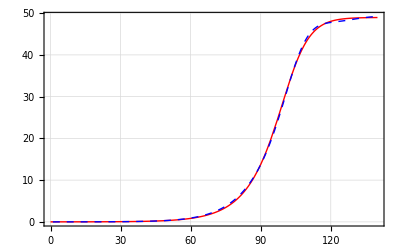

```mathematica
compare=Show[{p,simIn},PlotRange->All,Frame->True,GridLines->Automatic]
```

```mathematica
z1t=functofit/.x->t/.param
```

(0.00280182 ⅇ^(0.0948893 t))/(√(1+3.27329×10^-9 ⅇ^(0.189779 t)))

#### Fitting the equations with z1 and z2 equations

```mathematica
plt=ListLinePlot[{Table[-1/Pi NIntegrate[Cos[x]bsol[t,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,0,T,5}],Table[-1/Pi NIntegrate[Cos[2x]bsol[t,x],{x,-Pi,Pi},PrecisionGoal->4,AccuracyGoal->5,Method->{Automatic,"SymbolicProcessing"->0}],{t,0,T,5}]},PlotRange->All,PlotStyle->{{Thick,Dashed,Blue},{Thick,Dashed,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14}];
```

```mathematica
T2=140;
```

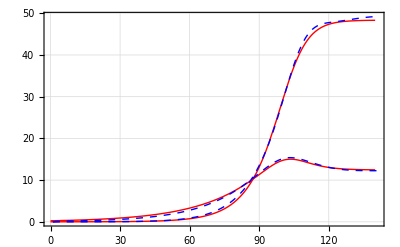

```mathematica
sol=NDSolve[{z1'[t]==p1 z1[t]-p2 z1[t](z1[t]^2+2z2[t]^2)-2γ z1[t] z2[t],z2'[t]==λ2 z2[t]-p2 z2[t](2z1[t]^2+z2[t]^2)-γ z1[t]^2,z1[0]==r0,z2[0]==0.25}/.{r0->0.003,p1->0.09,p2->0.000042,λ2->0.043,γ->-0.00085},{z1,z2},{t,0,T2}];
r1r2dyn=Show[Plot[Evaluate[{z1[t]/.sol,z2[t]/.sol}],{t,0,T2},PlotStyle->{{Thick,Red},{Thick,Red}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14},PlotRange->All],plt]
```

#### Pattern fit in physical space

```mathematica
{t1,t2,t3}={90,110,130}
```

{90,110,130}

```mathematica
z1[t]/.{{t->t1},{t->t2},{t->t3}}/.sol
```

{{13.1345,42.9054,48.1758}}

```mathematica
{c1,c2,c3}=1/(2Pi) NIntegrate[bsol[5{t1,t2,t3},x],{x,-Pi,Pi}]
```

{7.88858,35.3811,37.8596}

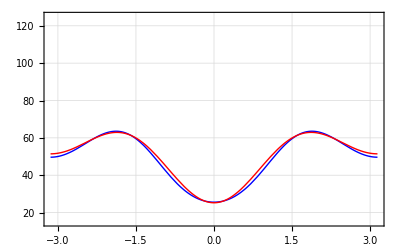

```mathematica
plt1=Plot[{b0+bsol[t,x]/.t->5t1-5/.fp,c1+b0-z1[t]Cos[x]-z2[t]Cos[2x]+(0.00001z1[t]^3+0.0001z1[t]z2[t])Cos[3x]/.fp/.sol/.t->t1},{x,-Pi,Pi},BaseStyle->{FontFamily->"CMU Serif",14},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,PlotRange->{15,125}]
```

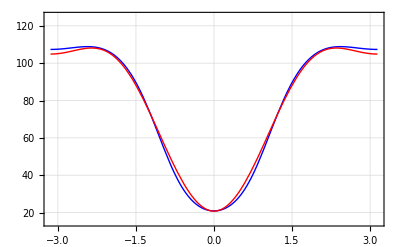

```mathematica
plt2=Plot[{b0+bsol[t,x]/.t->5t2/.fp,c2+b0-z1[t]Cos[x]-z2[t]Cos[2x]+(0.00001z1[t]^3+0.0001z1[t]z2[t])Cos[3x]/.fp/.sol/.t->t2},{x,-Pi,Pi},BaseStyle->{FontFamily->"CMU Serif",14},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,PlotRange->{15,125}]
```

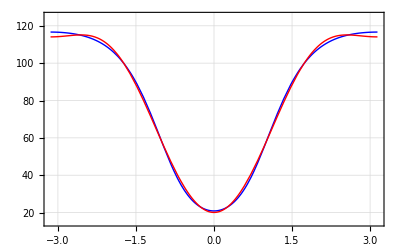

```mathematica
plt3=Plot[{b0+bsol[t,x]/.t->5t3/.fp,c3+b0-z1[t]Cos[x]-z2[t]Cos[2x]+(0.00001z1[t]^3+0.0001z1[t]z2[t])Cos[3x]/.fp/.sol/.t->t3},{x,-Pi,Pi},BaseStyle->{FontFamily->"CMU Serif",14},PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,GridLines->Automatic,PlotRange->{15,125}]
```

#### r1r2 streamplot

```mathematica
θ=Table[Pi/2*(1-Exp[-0.8t/2]),{t,0,20,1}]//N;
```

```mathematica
r=5;
initialcondition=Table[{z1[0]==r Cos[θ[[i]]],z2[0]==r Sin[θ[[i]]]},{i,Dimensions[θ][[1]]}];
```

```mathematica
z1z2param=Thread[{r0,p1,p2,λ2,γ}->{0.003,0.09,0.000042,0.043,-0.00085}]
```

{r0→0.003,p1→0.09,p2→0.000042,λ2→0.043,γ→-0.00085}

```mathematica
solpp=Table[NDSolve[Flatten[{z1'[t]==p1 z1[t]-p2 z1[t](z1[t]^2+2z2[t]^2)-2γ z1[t] z2[t],z2'[t]==λ2 z2[t]-p2 z2[t](2z1[t]^2+z2[t]^2)-γ z1[t]^2,initialcondition[[i]]}]/.z1z2param,{z1,z2},{t,0,2000}],{i,Dimensions[initialcondition][[1]]}];
```

```mathematica
sol2pp=NDSolve[{z1'[t]==p1 z1[t]-p2 z1[t](z1[t]^2+2z2[t]^2)-2γ z1[t] z2[t],z2'[t]==λ2 z2[t]-p2 z2[t](2z1[t]^2+z2[t]^2)-γ z1[t]^2,z1[0]==0.1,z2[0]==2}/.z1z2param,{z1,z2},{t,0,2000}];
```

```mathematica
pp1=ParametricPlot[Table[{z1[10t],z2[10t]}/.solpp[[i]],{i,Dimensions[initialcondition][[1]]}],{t,0,200},PlotRange->All,Frame->True,PlotStyle->{Thickness[0.002],Gray},GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif",14},AspectRatio->True]/.Line[x_]:>{Arrowheads[ConstantArray[0.02,3]],Arrow[x]};
```

```mathematica
pp2=ParametricPlot[{z1[10 t],z2[10 t]}/. sol2pp,{t,0,80},PlotRange->All,AspectRatio->True,Frame->True,PlotStyle->{RGBColor[0,0.6,0]}]/.Line[x_]:>{Arrowheads[ConstantArray[0.025,15]],Arrow[x]} ;
```

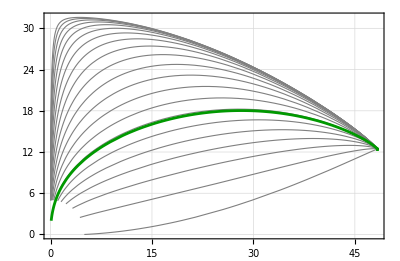

```mathematica
parameticplt=Show[pp1,pp2]
```